```mathematica
Quit[]
```

```mathematica
TT2p42PL=Import["/home/jortecal/GitHub/eRosita/PuntsMarcoFullRange_24_dblpwl/Results_Marco/CombinedProfiles/CombinedBounds.dat","Table","FieldSeparators"->{" "},"HeaderLines"->1];
IBounds12p42PL=Interpolation[Table[{TT2p42PL[[i,1]],TT2p42PL[[i,2]]},{i,1,Length[TT2p42PL]}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
TT2p42PLJ=Import["/home/jortecal/GitHub/eRosita/Full_Range_24_dblpwl/Results/CombinedProfiles/CombinedBounds.dat","Table","FieldSeparators"->{" "},"HeaderLines"->1];
IBounds12p42PLJ=Interpolation[Table[{TT2p42PLJ[[i,1]],TT2p42PLJ[[i,2]]},{i,1,Length[TT2p42PLJ]}],InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {1.10001} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

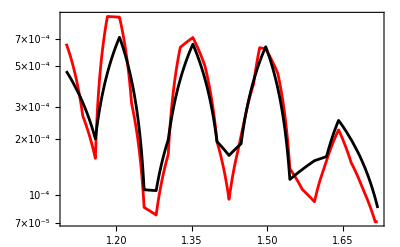

```mathematica
LogPlot[{IBounds12p42PLJ[x],IBounds12p42PL[x]},{x,1.1,1.72},Frame->True,PlotStyle->{Red,Black}]
```

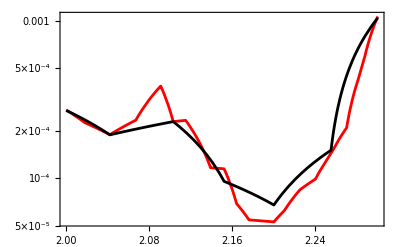

```mathematica
LogPlot[{IBounds12p42PLJ[x],IBounds12p42PL[x]},{x,2.,2.3},Frame->True,PlotStyle->{Red,Black}]
```

```mathematica
IBounds12p42PL[1.2]
```

0.000651385

```mathematica
ratio2p42PLtoB1PL={};
Diff2p42PLtoB1PL={};
Do[
En=TT2p42PL[[i,1]];
B2p42PL=IBounds12p42PL[En];
B2p42PLJ=IBounds12p42PLJ[En];
Print[En," ",B2p42PL/B2p42PLJ," ",(B2p42PL-B2p42PLJ)/(B2p42PL+B2p42PLJ)2.];
AppendTo[ratio2p42PLtoB1PL,{En,B2p42PL/B2p42PLJ}];
AppendTo[Diff2p42PLtoB1PL,{En,(B2p42PL-B2p42PLJ)/(B2p42PL+B2p42PLJ)2.}];
,{i,1,Length[TT2p42PL]}]
```

1.109 0.76789 -0.262585

1.158 1.27585 0.242417

1.206 0.777848 -0.249911

1.255 1.24684 0.219718

1.279 1.35741 0.30322

1.303 1.20158 0.18312

1.352 0.92004 -0.08329

1.4 1.00069 0.000691191

1.424 1.73581 0.537911

1.448 0.938614 -0.0633299

1.497 1.028 0.0276152

1.545 0.873014 -0.135595

1.594 1.67126 0.502581

1.618 1.05343 0.0520415

1.642 1.12587 0.118414

1.727 0.974656 -0.0256689

1.764 0.914441 -0.0893827

1.8 1.00114 0.00114234

1.848 0.994014 -0.006004

1.897 1.02428 0.0239917

1.945 0.992249 -0.00778166

2. 0.992905 -0.00711994

2.042 0.998123 -0.00187836

2.103 0.999759 -0.00024133

2.152 0.832267 -0.183088

2.2 1.27977 0.245439

2.255 1.05665 0.0550871

2.3 0.978991 -0.0212324

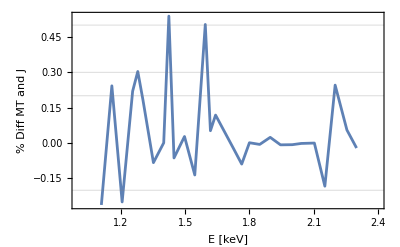

```mathematica
ListPlot[Diff2p42PLtoB1PL,Joined->True,Frame->True,PlotRange->{{1,2.4},Automatic},GridLines->{None,{-1.0,-0.5,-0.3,-0.2,0.2,0.3,0.5,1.0}},Frame->True,FrameLabel->{"E [keV]","% Diff MT and J"}]
```